## Introduction

Coolest function ever made, references the cell directly above

```mathematica
«:=Out[
ToExpression[
StringCases[
ToString[PreviousCell[CellStyle->"Output"]//NotebookRead//Last],
"Out["~~d:DigitCharacter..~~"]":>d][[1]]
]
]
```

Import the data from the elliptic solver, but remove the last point which corresponds to spatial infinity

```mathematica
(* import the CSV file *)
data=Import[
"/home/undercover/projects/cactus/repos/magnetoscalar/MagScalarInit/etc/QHairyBH/alpha=0.1_q=0.3385_mu=1_gamma=3.97887/upper/rh=0.2000/w=0.700/output.csv"
];

(* TODO: fetch this from the file automatically *)
q=0.3385;
rh=0.2;
ω=0.7;
c=1;

(* remove all comments from CSV file *)
data=Select[data,!StringStartsQ[ToString[#[[1]]],"#"]&];

(* fetch data *)
(* [[All,i]] -> fetches all elements from column i *)
(* [[2;;Length[arr]-1]] -> slice 1D array to go from 2nd element to the N-1 *)
x=data[[All,1]];
x=x[[2;;Length[x]-1]];
F1=data[[All,2]];
F1=F1[[2;;Length[F1]-1]];
F0=data[[All,4]];
F0=F0[[2;;Length[F0]-1]];
dF0=data[[All,5]];
dF0=dF0[[2;;Length[dF0]-1]];
ϕ=data[[All,6]];
ϕ=ϕ[[2;;Length[ϕ]-1]];
V=data[[All,8]];
V=V[[2;;Length[V]-1]];
dV=data[[All,9]];
dV=dV[[2;;Length[dV]-1]];

 (* total length of each vector *)
Nt=Length[x];
```

```mathematica
r=(rh+c x)/(1-x);
```

Make a plot of V'[r_h]to see what it looks like

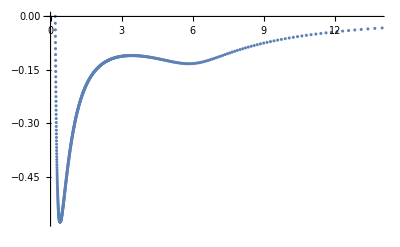

```mathematica
ListPlot[
Transpose[{r,dV}]
]
```

From my computations, the charge Q as a function of the radius is
	Q=-ⅇ^(F_1-F_0)(r+r_h)^3/(r-r_h)V'

Since V'[r_h]=0, the value of the charge of the horizon Q_h is given by the limit
	Q_h=-8 r_h^3 ⅇ^(F_1[r_h]-F_0[r_h])lim_(r->r_h) V'/(r-r_h)

As for the total charge, its given by the limit
	Q_T=-lim_(r->∞) r^2 V'

There’s also the fact that the total charge is the sum of two contributions
	Q_T=Q_h+Q_ϕ
where
	Q_ϕ=qQ_N
with q the coupling constant and Q_N the Noether charge of the scalar field

You can also compute the charge of the scalar field as
	Q_ϕ=-2q∫_r_h^∞ (ⅇ^(3 F_1-F_0)(r+r_h)^7(ω-qV)ϕϕ^*)/(r^4(r-r_h))ⅆr

## Computing Charge at the Horizon

Analytically we expect that V'[r_h]=0, but this is not satisfied numerically.
Therefore, to compute the limit, we’re going to select a few points close to r=r_h and fit a curve on V'[r] enforcing that V'[r_h]=0.

```mathematica
(* number of points to select *)
n = 50;
```

```mathematica
(* fit a curve and show its expression *)
model=NonlinearModelFit[
Transpose[{r,dV}][[1;;n]],
c1(R-rh)+c2(R-rh)^2+c3(R-rh)^3+c4(R-rh)^4,
{c1,c2,c3,c4},
R
];

dVfit=model["BestFit"]
```

-9.65603 (-0.2+R)+70.4431 (-0.2+R)^2-299.401 (-0.2+R)^3+638.689 (-0.2+R)^4

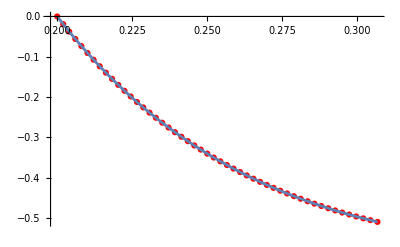

```mathematica
(* show the fit graphically to see whether it is good enough *)
Show[
ListPlot[
Transpose[{r,dV}][[1;;n]],
PlotStyle->Red
],
Plot[
dVfit/.R->Rval,
{Rval, r[[1]], r[[n]]}
]
]
```

Computing the value of Q_h using the limit above

```mathematica
Qh=-8 rh^3 ⅇ^(F1[[1]]-F0[[1]])lim_(R->rh) dVfit/(R-rh)
```

0.653764

## Computing Total Charge and Mass

Instead of computing the limit, we are going to take the highest values we have available, to compute the total charge Q_T. Note that In [Herdeiro2020], this quantity is called Q_e.

```mathematica
QT=-ⅇ^(F1[[Nt]]-F0[[Nt]])(r[[Nt]]+rh)^3/(r[[Nt]]-rh)dV[[Nt]]
```

6.81475

Given that the total charge is Q_T=Q_H+Q_ϕ, then the charge of the electric field must be

```mathematica
Qϕ=QT-Qh
```

6.16098

The Komar mass, computed at the furthest point we have, is

```mathematica
MK=ⅇ^(F0[[Nt]]+F1[[Nt]])(2rh+(r[[Nt]]^2-rh^2)dF0[[Nt]])
```

0.539042

## Estimate of radius for the hair

Create an interpolating function with Q_ϕ[R] as a function of the isotropic radius R

```mathematica
Q=Interpolation[
Table[
{r[[i]],-ⅇ^(F1[[i]]-F0[[i]])(r[[i]]+rh)^3/(r[[i]]-rh)dV[[i]]-Qh},
{i,2,Length[r]}  (* remove value at the horizon because of 1/0 *)
]
];
```

Now find the value of the radius R which has a specific percentage of the total hair

```mathematica
NSolve[
Q[R]/Qϕ==0.01,
R
]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{R→1.15949}}

```mathematica
NSolve[
Q[R]/Qϕ==0.99,
R
]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{R→7.77057}}

## Computing charge of the scalar field

In here I’m computing the charge of the scalar field as a volume integral.
This is only relevant to double check the computation above where I computed the total charge and the charge of the BH, and then used that to compute the charge of the scalar field.

Given that there’s a division by 0 at r=r_h, we approximate the function V by a Taylor series that is V[r_h]=ω/q and avoid the indetermination in the computation of the integral

```mathematica
(* number of points to select *)
n2 = 50;
```

```mathematica
(* N.ba of coefficients in Taylor series *)
Ncoef=10;
coef=Array[Symbol["c"<>ToString[#]]&,Ncoef];

(* fit a curve and show its expression *)
model2=NonlinearModelFit[
Transpose[{r,V}][[1;;n2]],
ω/q+∑_(i=2)^Ncoef coef[[i]](R-rh)^i,
coef,
R
];

Vfit=model2["BestFit"];
```

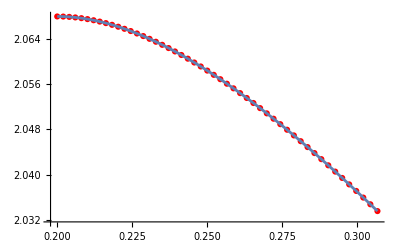

```mathematica
(* show the fit graphically to see whether it is good enough *)
Show[
ListPlot[
Transpose[{r,V}][[1;;n2]],
PlotStyle->Red
],
Plot[
Vfit/.R->Rval,
{Rval, r[[1]], r[[n2]]}
]
]
```

Interpolate the numerical quantities to compute the integral

```mathematica
IF0=Interpolation[Transpose[{r,F0}][[1;;Nt]]];
IF1=Interpolation[Transpose[{r,F1}][[1;;Nt]]];
Iϕ=Interpolation[Transpose[{r,ϕ}][[1;;Nt]]];
IV=Interpolation[Transpose[{r,V}][[1;;Nt]]];
```

Compute the integral with far-away solution plus near horizon solution

```mathematica
NIntegrate[
-2q (ⅇ^(3IF1[R]-IF0[R])(R+rh)^7(ω-q IV[R])Iϕ[R]^2)/(R^4(R-rh)),
{R,r[[n2+1]],r[[Nt]]}
]
```

-6.15812

```mathematica
«+NIntegrate[
-2q (ⅇ^(3IF1[R]-IF0[R])(R+rh)^7(ω-q Vfit)Iϕ[R]^2)/(R^4(R-rh)),
{R,r[[1]],r[[n2]]}
]
```

-6.15937